# Trefoil Art

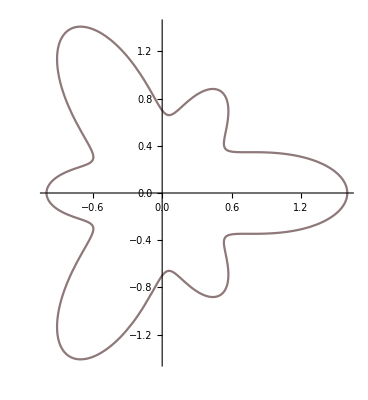

```mathematica
ParametricPlot[{Cos[t],Sin[t]}(1+0.3Cos[3t]+0.3Cos[6t]),{t,0,2π},PlotStyle->{Orange,Specularity[White,40]},ColorFunction->({x,y,u}|->Hue[u])]
```

```mathematica
KnotData[{3,1},"SpaceCurve"][t]
```

{Sin[t]+2 Sin[2 t],Cos[t]-2 Cos[2 t],-Sin[3 t]}

```mathematica
ParametricPlot3D[{Sin[t]+2 Sin[2 t],Cos[t]-2 Cos[2 t],-Sin[3 t]},{t,0,2π}]
```

-Graphics3D-

```mathematica
c=KnotData[{3,1},"SpaceCurve"];n=Simplify@FrenetSerretSystem[c[u],u][[-1,2;;]];ParametricPlot3D[{3c[u]+RotationMatrix[7u].{Cos[v],Sin[v]}.n(1+.3Cos[3v]+0.3Cos[6v])},{u,0,2Pi},{v,0,2Pi},PlotPoints->50,ColorFunction->(Hue[#5]&),PlotStyle->{MaterialShading["Glazed"]},Lighting->"ThreePoint",Mesh->None,ViewPoint->{1,0,2}]
```

-Graphics3D-

```mathematica
RotationMatrix[t]
```

{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}

```mathematica
{13,14,2}×{4,11,23}
```

{300,-291,87}

```mathematica
x=Cos;y=Sin;c=KnotData[{3,1},"SpaceCurve"]@u;n=FrenetSerretSystem[c,u][[-1,2;;]];ParametricPlot3D[9c+RotationMatrix[5u].{x@v,y@v}.n(3+x[3v]+x[6v]),{u,0,2Pi},{v,0,2Pi},PlotStyle->MaterialShading@{"Glazed",Pink},Lighting->"ThreePoint",Mesh->None,PlotPoints->50,ViewPoint->Top]
```

-Graphics3D-

```mathematica
c
```

{Sin[u]+2 Sin[2 u],Cos[u]-2 Cos[2 u],-Sin[3 u]}

```mathematica
%//FullSimplify
```

$Aborted

```mathematica
x=Cos;y=Sin;c=KnotData[{3,1},"SpaceCurve"]@u;n=FrenetSerretSystem[c,u][[-1,2;;]];ParametricPlot3D[9c+RotationMatrix[5u].{x@v,y@v}.n(3+x[3v]+x[6v]),{u,0,2Pi},{v,0,2Pi},PlotStyle->MaterialShading@"Glazed",Lighting->"ThreePoint",Mesh->None,PlotPoints->50,ViewPoint->Top]
```

-Graphics3D-

```mathematica
c=KnotData[{8,8}]
```

-Graphics3D-

```mathematica
c=KnotData[{8,18}]
```

-Graphics3D-